```mathematica
myRange = Range[32];
If[PrimeQ[#], Framed@Style[#, Orange, Bold, 14],#] &/@ myRange
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32}

```mathematica
x=DeleteDuplicates[1 + RandomInteger[#]&/@myRange]
```

{2,1,3,5,4,7,6,14,17,9,18,16,23,22,19,15,21,10}

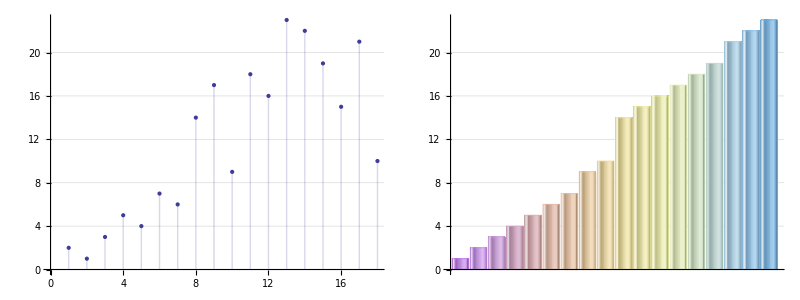

```mathematica
g1 = Show[ListPlot[x, GridLines->{None, Automatic}, GridLinesStyle->LightGray, Filling->Axis]];
g2 = Show[BarChart[Sort[x], ChartElementFunction->"GlassRectangle",ChartStyle->"Pastel",
GridLines->{None, Automatic}, GridLinesStyle->LightGray]];
Grid[{{g1, g2}}, ItemSize->{{20, 20}}, Frame->All, FrameStyle->LightGray]
```

```mathematica
DeleteCases[DeleteDuplicates[Table[If[PrimeQ[b], b, False],{b, 0, 32}]], False]
```

{2,3,5,7,11,13,17,19,23,29,31}

```mathematica
Manipulate[
Plot[Sin[x*a]Cos[x*b],{x,-Pi,Pi},Filling->filling],
{{a,-10,"Sin"},-10,10},{{b,-8.85,"Cos"}, -10, 10},{ {filling,None,"Axis filling"},{Axis,None},ControlType->RadioButton},
SaveDefinitions->True
]
```